```mathematica
SetDirectory[NotebookDirectory[]];
mat2 = Import["Displacements.txt","Table"];
```

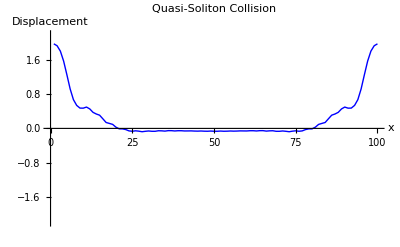

```mathematica
ListPlot[mat2[[All,390]],PlotJoined->True,PlotRange-> {-2.2,2.2}, PlotStyle-> Blue,AxesLabel-> {x,Displacement},PlotLabel->"Quasi-Soliton Collision"]
```

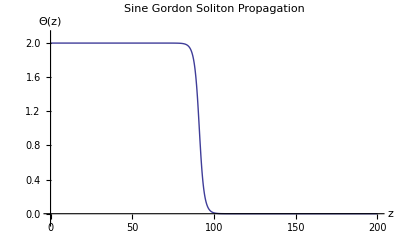

```mathematica
v = 2.667; (*Computed from the x-t diagram*)
co =√10; 
wo=(π*0.264911)^0.5; (*Max amplitude in Sine fit*)
u[z_] := 4/π ArcTan[Exp[-wo/co (z-91)/(√(1-(v/co)^2))]]
Plot[u[z],{z,0,200},PlotRange-> {-0.1,2.1}, PlotLabel->"Sine Gordon Soliton Propagation", AxesLabel-> {z,Θ[z]}]
```

```mathematica
Needs["PlotLegends`"]
Show[Plot[u[z],{z,0,200},PlotRange-> {-0.1,2.1}, PlotLabel->"Sine Gordon Quasi-Soliton Propagation", AxesLabel-> {"Position (x)","Displacement (u[x,t])"}],ListPlot[mat2[[All,327]],PlotJoined->True,PlotRange-> {-0.1,2.2}, PlotStyle-> Red,AxesLabel-> {"Position (x)","Displacement (u(x,t))"},PlotLabel->"Sine Gordon Quasi-Soliton Propagation at a certain time instant"]]
```

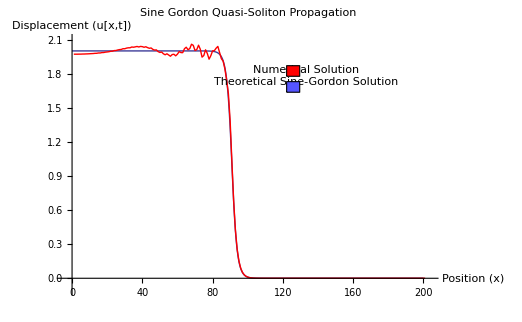

```mathematica
Needs["PlotLegends`"]
ListContourPlot[Transpose[mat2],Axes-> True, FrameLabel-> {"Position(x)", "Time(t)"},PlotLabel-> {"X-T contour plot of displacements"}]
```

-Graphics-

```mathematica
plots=Table[ListPlot[mat2[[All,2i]],PlotJoined->True,PlotRange-> {-1,4}],{i,1,170}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export["collision_animation.avi",plots]
```

collision_animation.avi